-Graphics-
-Graphics-
-Graphics-

```mathematica
Lk=5;(*倒空间大小,2Lk+1维的矩阵*)
a=1;(*晶格常数*)
b1=(2Pi)/a;(*单位倒格矢*)
```

-Graphics-

```mathematica
(*动能项的构造*)
list1=Table[(n*b1+kx)^2/2,{n,-Lk,Lk}];
M=DiagonalMatrix[list1];
```

```mathematica
(*势场的傅里叶系数*)
V=DiracDelta[x/(2Pi)];
coff=Table[FourierCoefficient[1.V,x,i],{i,-2Lk,2Lk}]
center=(Length[coff]+1)/2;
Table[{M[[i,j]]=M[[i,j]]+coff[[center+j-i]]},{j,1,2Lk+1},{i,1,2Lk+1}];
M//TraditionalForm
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(1/2 (kx-10 π)^2+1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1/2 (kx-8 π)^2+1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1/2 (kx-6 π)^2+1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1/2 (kx-4 π)^2+1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1/2 (kx-2 π)^2+1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | kx^2/2+1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1/2 (kx+2 π)^2+1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1/2 (kx+4 π)^2+1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1/2 (kx+6 π)^2+1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1/2 (kx+8 π)^2+1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1/2 (kx+10 π)^2+1.)

```mathematica
Table[Subscript[Ek, i]=Eigenvalues[M][[i]],{i,1,4}];
```

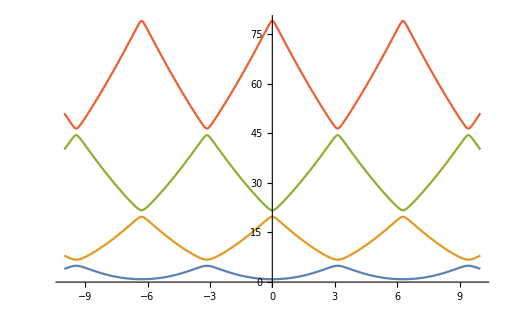

```mathematica
Plot[{Subscript[Ek, 1],Subscript[Ek, 2],Subscript[Ek, 3],Subscript[Ek, 4]},{kx,-10,10}]
```